```mathematica
filenames={
"Table_Deterministic_control3_selfing0_sexualReproduction1_seedbank1_cost300_kCost5_kHerb5.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost5_kHerb5.txt"
};
{rwcol,rrcol,wwcol}={RGBColor["#F2A35E"],RGBColor["#BF766F"],RGBColor["#7C92A6"]}
{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

```mathematica
makeplot[datafile_]:={ListLogPlot[{datafile⟦2;;,5⟧,datafile⟦2;;,6⟧,datafile⟦2;;,7⟧}/10^4,Mesh->True,MeshStyle->PointSize[0.018],Joined->True,Frame->True,PlotRange->{Automatic,{10^-9,10^3}},PlotStyle->{Directive[Full,wwcol],Directive[Full,rwcol],Directive[Full,rrcol]},FrameStyle->Directive[Black,Thickness[0.003],FontSize->12],FrameLabel->{Style["Time(Years)",Black,16],Style["Plants / m^2",Black,16]},ImageSize->Large]}
```

```mathematica
Manipulate[makeplot[data⟦i⟧]⟦1⟧,{i,1,Length[filenames],1}]
```

## Seeds

```mathematica
makeplotseeds[datafile_]:={ListLogPlot[{datafile⟦2;;,8⟧,datafile⟦2;;,9⟧,datafile⟦2;;,10⟧}/10^4,Mesh->True,MeshStyle->PointSize[0.018],Joined->True,Frame->True,PlotRange->{Automatic,{10^-8,10^5}},PlotStyle->{Directive[Full,wwcol],Directive[Full,rwcol],Directive[Full,rrcol]},FrameStyle->Directive[Black,Thickness[0.003],FontSize->12],FrameLabel->{Style["Time(Years)",Black,16],Style["Seeds / m^2",Black,16]},ImageSize->Large]}
```

```mathematica
Manipulate[makeplotseeds[data⟦i⟧]⟦1⟧,{i,1,Length[filenames],1}]
```

## selfing/notselfing

```mathematica
moredata=Import[NotebookDirectory[]<>"../Data/"<>"Table_Equilibrium_tillage0.txt","CSV"]
```

{{Cost,Het,R,WW,RW,RR},{0.001,0,0.00001002,0.99999,3.99996×10^-8,0.00001},1998,{0.4,1,2.5×10^-8,1.,2.85714×10^-8,1.07143×10^-8}}
 |  |  |  |

## Notselfing

```mathematica
pos=Position[moredata⟦All,{1,2}⟧,{0.3,0.5}]⟦1,1⟧;
```

```mathematica
onlyplants=data⟦1⟧⟦2;;,{5,6,7}⟧
```

{{3693.79,0.00479831,0.0067066},{2658.21,1.83985,0.117842},{2530.17,234.052,2.1634},{2449.91,25784.3,1015.38},{1800.47,641450.,492857.},{568.272,604587.,1.29403×10^6},{245.941,405774.,1.5747×10^6},{114.42,279684.,1.72611×10^6},{54.7953,195420.,1.821×10^6},{26.609,137435.,1.88426×10^6},{13.027,96987.5,1.92765×10^6},{6.41405,68579.3,1.95784×10^6},{3.1722,48551.7,1.97901×10^6},{1.57463,34400.5,1.99392×10^6},{0.783989,24387.1,2.00445×10^6},{0.391312,17294.9,2.01191×10^6},{0.195711,12268.5,2.01718×10^6},{0.0980429,8704.45,2.02093×10^6},{0.0491789,6176.58,2.02358×10^6},{0.0246937,4383.23,2.02546×10^6},{0.0124091,3110.77,2.02679×10^6},{0.00623967,2207.81,2.02774×10^6},{0.003139,1567.,2.02841×10^6},{0.00157972,1112.21,2.02889×10^6},{0.000795228,789.429,2.02923×10^6},{0.000400401,560.329,2.02947×10^6},{0.000201636,397.72,2.02964×10^6},{0.000101553,282.302,2.02976×10^6},{0.0000511518,200.379,2.02985×10^6},{0.0000257666,142.23,2.02991×10^6}}

```mathematica
plantsformula=(onlyplants⟦All,2⟧+2 onlyplants⟦All,3⟧)/(2 (onlyplants⟦All,1⟧+onlyplants⟦All,2⟧+onlyplants⟦All,3⟧));
```

```mathematica
notselfing=PrependTo[plantsformula ,moredata⟦pos⟧⟦3⟧]
```

{4.2029×10^-8,2.46514×10^-6,0.000390112,0.0430848,0.475478,0.716114,0.840531,0.897445,0.930228,0.951517,0.965997,0.976042,0.983076,0.988025,0.991519,0.993989,0.995738,0.996977,0.997856,0.998478,0.99892,0.999234,0.999456,0.999614,0.999726,0.999806,0.999862,0.999902,0.99993,0.999951,0.999965}

## Selfing

```mathematica
pos=Position[moredata⟦All,{1,2}⟧,{0.3,0.5}]⟦1,1⟧;
```

```mathematica
onlyplants=data⟦2⟧⟦2;;,{5,6,7}⟧
```

{{3693.79,0.00479831,0.0067066},{2658.22,0.359417,1.34139},{2530.25,34.7924,243.786},{2431.66,4140.44,42135.8},{602.384,53077.5,1.5162×10^6},{98.0127,26613.3,1.94138×10^6},{39.5108,13733.4,1.99723×10^6},{18.459,7521.97,2.01572×10^6},{9.21801,4199.25,2.02328×10^6},{4.79172,2359.76,2.02668×10^6},{2.55816,1329.22,2.02831×10^6},{1.39081,749.383,2.02913×10^6},{0.765563,422.622,2.02956×10^6},{0.424926,238.371,2.02978×10^6},{0.237168,134.455,2.0299×10^6},{0.132859,75.8413,2.02997×10^6},{0.0746057,42.7798,2.03001×10^6},{0.04196,24.1308,2.03003×10^6},{0.0236235,13.6115,2.03004×10^6},{0.013309,7.67789,2.03005×10^6},{0.00750121,4.33089,2.03005×10^6},{0.00422903,2.44293,2.03005×10^6},{0.00238467,1.37799,2.03006×10^6},{0.00134484,0.777287,2.03006×10^6},{0.000758477,0.438446,2.03006×10^6},{0.000427797,0.247315,2.03006×10^6},{0.000241294,0.139504,2.03006×10^6},{0.000136102,0.0786902,2.03006×10^6},{0.0000767695,0.044387,2.03006×10^6},{0.0000433029,0.0250375,2.03006×10^6}}

```mathematica
plantsformulaselfing=(onlyplants⟦All,2⟧+2 onlyplants⟦All,3⟧)/(2 (onlyplants⟦All,1⟧+onlyplants⟦All,2⟧+onlyplants⟦All,3⟧));
```

```mathematica
selfing=PrependTo[plantsformulaselfing ,moredata⟦pos⟧⟦3⟧]
```

{4.2029×10^-8,2.46514×10^-6,0.000571858,0.092986,0.907574,0.982711,0.993189,0.996566,0.998132,0.99896,0.999416,0.999671,0.999815,0.999896,0.999941,0.999967,0.999981,0.999989,0.999994,0.999997,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
selfing//Length
```

31

## Plot

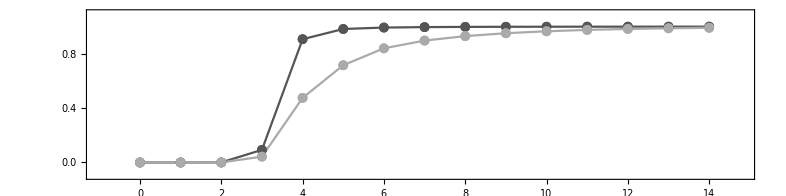

```mathematica
ListPlot[{selfing⟦1;;15⟧,notselfing⟦1;;15⟧},Joined->True,PlotRange->{{-1,14.8},{-0.1,1.1}},Frame->True,DataRange->{0,14},Mesh->Full,MeshStyle->PointSize[0.009],PlotStyle->{Lighter[Black],Lighter[Gray]},AspectRatio->0.25,FrameStyle->Directive[Black,Thickness[0.002]]]
```